# Directed-Graph Iterated Function Systems

by Mark McClure

Directed-graph iterated function systems are an important generalization of iterated function systems.  In this article, we discuss their basic theory and implementation.

## Introduction

Consider the curve in the plane K  shown in Figure 1.  K  is called the Koch curve and is an example of a self-similar set.  Figure 1 shows how K is composed of 4 copies of itself, each scaled by a factor of 1/3.  More generally, a self-affine set is one composed of affine images of the whole set.  The terminology iterated function system, or IFS, was introduced by Barnsley to describe a process for rendering images of such sets.  There are many good references for IFSs including [Barnsley 1993], [Edgar 1990], and [Gutierrez, Iglesias, Rodriguez, and Rodriguez 1997] which describes an implementation in Mathematica.

In this article, we consider a generalization of self-similar sets and its implementation in Mathematica.  All of our functions are encapsulated in the package DigraphFractals.  Consider the two curves A and B shown in figure 2.  A is composed of 1 copy of itself, scaled by a factor 1/2, and 2 copies of B, rotated and scaled by a factor 1/2.  B is composed of 1 copy of itself, scaled by a factor 1/2, and 1 copy of A, reflected and scaled by a factor 1/2.  The sets A and B exhibit directed-graph self-similarity and may be described using a directed-graph iterated function system, or digraph IFS.  Our formulation of a digraph IFS first appeared in [Mauldin and Williams, 1988] and is also described in [Edgar 1990] and [Falconer 1997].

## Basic Theory

The first indgredient for a digraph IFS is a directed multi-graph which describes the combinatorics of how the pieces fit together.  A directed multi-graph G consists of a finite set V of vertices and a finite set E of directed edges between vertices.  G is called a multi-graph because we allow more than one edge between any two vertices.  Given two vertices, u and v, we denote the set of all edges from u to v by E_uv.  More generally, a path through G is a finite sequence of edges so that the terminal vertex of any edge is the initial vertex of the subsequent edge.  G is called strongly connected if for every u and v in V, there is a path from u to v.  We denote the set of all paths of length n with initial vertex u by E_u^n.

Figure 3 shows the directed multi-graph for the curves A and B.  There are two edges from node A to node B and one edge from node A to itself since A consists of two copies of B together with one copy of itself.  Similarly, there is one edge from node B to node A and one edge from B to itself since B consists of one copy of A together with one copy of itself.

Note that the edges in figure 3 are labeled.  In general, we obtain a digraph IFS from a directed multi-graph by associating an affine function f_e with each edge e of the digraph.  There are two main types of functions we will consider.  A function f:ℝ^n→ℝ^n is called a similarity transformation, or simply a similarity, if there is an r>0, called the similarity ratio of f, such that |f(x)-f(y)|=r|x-y| for all x in ℝ^n.  More generally, an affine transformation is a linear transformation plus a translation.  The labels in figure 3 correspond to the following affine functions, which are in fact similarities.

a_1(x) = (1/2 | 0
0 | 1/2)x+ (1/4
(√3)/4)          a_2(x) = (1/2 | -(√3)/2
(√3)/2 | 1/2)x
a_3(x) = (1/2 | (√3)/2
-(√3)/2 | 1/2)x+ (3/4
(√3)/4)
b_1(x) = (1/2 | 0
0 | -1/2)x+ (1/2
0)          b_2(x) = (1/2 | 0
0 | 1/2)x

An affine transformation need not scale a set by the same amount in all directions.  However, we may characterize its largest scaling factor by the spectral radius of the linear part, which is the maximum of the absolute values of all its complex eigenvalues.  A digraph IFS is called contractive if the product of the scaling factors in any closed loop is less than 1.  Theorem 4.3.5 of [Edgar 1990] states that for any contracting digraph IFS, there is a unique set of closed, bounded sets K_v, one for every v in V, such that for every u in V,

K_u = ∪_(vϵV,eϵE_uv)f_e(K_v).

Such a collection of sets is called the invariant list of the digraph IFS and we will refer to its members as digraph fractals.  Note that an IFS is the special case of a digraph IFS with one node and theorem 4.3.5 of [Edgar 1990] is a generalization of the statement that a unique invariant set exists for a contractive IFS.

## Implementation of a Deterministic Algorithm

In this section, we implement a deterministic algorithm to generate the sets A and B.  The first step is to determine an appropriate data structure to describe a digraph IFS.  For this purpose, we will use an adjacency matrix of lists of affine functions.  The element in row u and column v will be a list of affine functions which map E_v into E_u.  Each affine function will be described by a pair {A,b}, where A is a two dimensional matrix indicating the linear part and b is a two dimensional vector indicating the shift.  Here is the code describing the digraph IFS for the curves A and B.

```mathematica
rotate[θ_]:={{Cos[θ],-Sin[θ]},
	{Sin[θ],Cos[θ]}};
a1 = {{{1/2,0},{0,1/2}},{1/4,√3/4}};
a2 = {1/2 rotate[π/3], {0,0}};
a3 = {1/2 rotate[-π/3],{3/4,√3/4}};
b1 = {{{1/2,0},{0,-1/2}},{1/2,0}};
b2 = {{{1/2,0},{0,1/2}},{0,0}};
curvesDigraph = {{{a1},{a2,a3}},{{b1},{b2}}};
```

We also need an initial approximation to each digraph fractal for the digraph IFS to act upon.  In general, these could be any Graphics primitives, but some objects lead to more natural approximations than others.  Note that each initiator is a list of Graphics primitives. This way each initiator may be a fairly complicated graphic.  Here is our choice of initiators.

```mathematica
lineSegment = Line[{{0,0},{1,0}}];
initiators = {{lineSegment},{lineSegment}};
```

Each affine list needs to be transformed into a function which acts on the initiators.  The version of toFuncs used by the package takes Graphics primitives other than Line into account.

```mathematica
toFuncs[{A_,b_}] := Module[{fOut},
		fOut[{x_,y_}] := N[A.{x,y} + b]; 
		fOut[Line[x__]] := Line[fOut /@ x];
		fOut
	];
digraphFuncs = Map[toFuncs,curvesDigraph, {3}];
```

We now need to describe the action of the digraph IFS on the initiators to get to the next stage in the approximation.  Suppose that K_u^0 is the initiator for K_u.  Then by equation (1), we need to replace K_u^0with the union over all v ϵ V and e ϵ E_uvof f_e(K_v^0).  Now the element in row u and column v of our digraph IFS contains a list of all f_e for e ϵ E_uv.  Thus we need to apply all of the functions in this list to K_v^0 (using Outer) and take the union over all v ϵ V.  Note that this is practically matrix multiplication, or more correctly an inner product.  There is a complication.  The function Inner gives a generalized inner product which goes deeply into nested structures.  We will need to change the heads at the appropriate level to prevent this.  Taking all of this into account, we obtain the following code for the first step.

```mathematica
digraphFuncs = Apply[placeHolder, digraphFuncs, {2}];
initiators = Apply[placeHolder, initiators,{1}];
step = Inner[Outer[#1[#2]&, #1, #2]&, digraphFuncs, initiators,List];
```

This process is now repeated with step as the new input to get to the next stage.

```mathematica
step = Inner[Outer[#1[#2]&, #1, #2]&, digraphFuncs, step,List];
```

Note that step now holds a list of lists of graphics primitives held in placeholders.  To see the approximation we simply get rid of the placeholders and map Show onto the list.

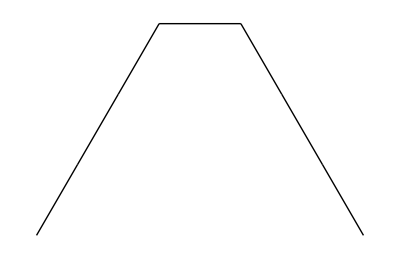
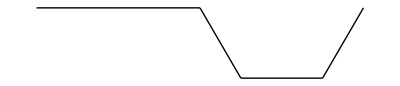

```mathematica
graphicList = step //. placeHolder[x___] -> {x};
Show[Graphics[#], AspectRatio -> Automatic]& /@ graphicList
```

Here is the next step.

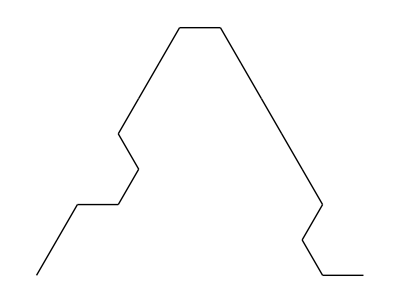
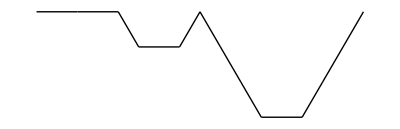

```mathematica
step = Inner[Outer[#1[#2]&, #1, #2]&, digraphFuncs, step,List];
graphicList = step //. placeHolder[x___] -> {x};
Show[Graphics[#], AspectRatio -> Automatic]& /@ graphicList
```

To see a higher order approximation, we simply Nest this procedure.

```mathematica
depth = 10;
graphicList = 
	Nest[Inner[Outer[#1[#2]&, #1, #2]&, digraphFuncs, #,List]&,
		initiators, depth] //. placeHolder[x___] -> {x};
Show[Graphics[#], AspectRatio -> Automatic]& /@ graphicList
```

-Graphics-

## Examples

The algorithm described in the previous section is encapsulated in our package function ShowDigraphFractals, which generates images in the plane.  In this section, we illustrate the use of this function with several more examples.  First, we load the DigraphFractals package.

```mathematica
Needs["FractalGeometry`DigraphFractals`"];
```

Here is the package description of the function ShowDigraphFractals.

```mathematica
?ShowDigraphFractals
```

ShowDigraphFractals[digraph_,depth_] generates the approximation to the digraph self similar sets defined by digraph to order depth using a deterministic algorithm. The digraph is represented by a matrix of lists of affine functions written in the form {{{a1,a2},{b1,b2}},{x0,y0}}.

### The Koch Snowflake

The Koch curve is an example of a self-similar set and may be realized as a special case of a digraph fractal.  More than this, three copies of the Koch curve form the boundary of a set known as the Koch snowflake.  Thus both sets together may be realized as the invariant list of the following digraph IFS.

```mathematica
c1 = {{{1/3,0},{0,1/3}},{0,0}};
c2= {rotate[π/3]/3,{1/3,0}};
c3 = {rotate[-π/3]/3,{1/2,√3/6}};
c4 = {{{1/3,0},{0,1/3}},{2/3,0}};
f1 = {{{1,0},{0,-1}},{0,0}};
f2 = {rotate[π/3],{0,0}};
f3 = {rotate[-π/3],{1/2,√3/2}};
Koch = {{{c1,c2,c3,c4},{}},{{f1,f2,f3},{}}};
ShowDigraphFractals[Koch,7, 
	Prolog -> {AbsolutePointSize[.4]}]
```

-Graphics-

A few observations are in order.  First, the digraph above is not strongly connected.  There is no path from the curve C to the flake F.  Nonetheless, F is a simple union of copies of C and ShowDigraphFractals works as expected.  Second, note that no initiators were specified.  The option Initiators may be used to define the initiators.  The default, Initiators→Automatic, uses the single point {0,0} as the initiator for each set.  Finally, note that ShowDigraphFractals accepts the usual Graphics options

### Heighway's Dragon

Heighway's dragon is a self-similar set in the plane.  It's boundary consists of the two digraph fractals defined here.  This time we use two vertical line segments as the initiators.

```mathematica
f1 = {{{1,0},{0,1}}.rotate[π/4]/√2,{0,0}};
f2 = {-rotate[-π/4]/√2,{0,1}};
g1 = {{{1/2,0},{0,1/2}},{0,0}};
g2 = {{{-1/2,0},{0,-1/2}},{0,1}};
heighwayDragon = {{{f1},{f2}},{{g1,g2},{}}};
lineSegment = Line[{{0,0},{0,1}}];
heighwayBoundary =ShowDigraphFractals[heighwayDragon,14,
	Initiators -> {{lineSegment},{lineSegment}},
	DisplayFunction -> Identity];
Show[GraphicsArray[heighwayBoundary]]
```

GraphicsArray::obs: GraphicsArray is obsolete. Switching to GraphicsGrid.

-Graphics-

Heighway's dragon boundary may be rendered by showing these two curves together.

```mathematica
Show[heighwayBoundary, 
	DisplayFunction -> $DisplayFunction]
```

-Graphics-

Alternatively, we could set up a non–strongly connected digraph IFS with this third set corresponding to the third node, just as we did for the Koch snowflake.

### Hilbert's Curve

Hilbert's space filling curve is a continuous function that maps the unit interval onto the unit square.  It turns out that the coordinate functions of this curve may be described using the following digraph IFS.

```mathematica
A = {{1/4,0}, {0,1/2}}; B = {{1/4,0}, {0,-1/2}};
f1 = {A,{0,0}}; f2 = {A,{1/4,0}};
f3 = {A,{1/2,1/2}}; f4 = {B,{3/4,1}};
g1 = {A,{0,0}}; g2 = {A,{1/4,1/2}};
g3 = {A,{1/2,1/2}};g4 = {B,{3/4,1/2}};
hilbertCurves = 
	{ {{f2,f3},{f1,f4}}, {{g1,g4},{g2,g3}} };
initiators = 
	{{Line[{{0,0},{1,1}}]},{Line[{{0,0},{1,0}}]}};
ShowDigraphFractals[hilbertCurves,6,
	Initiators -> initiators, Axes -> True]
```

-Graphics-

Note that the two initiators above were different.  In general we may use much more complicated initiators.  This may be used to illustrate the effect of the digraph IFS.  For example, consider the following initiators.

GraphicsArray::obs: GraphicsArray is obsolete. Switching to GraphicsGrid.

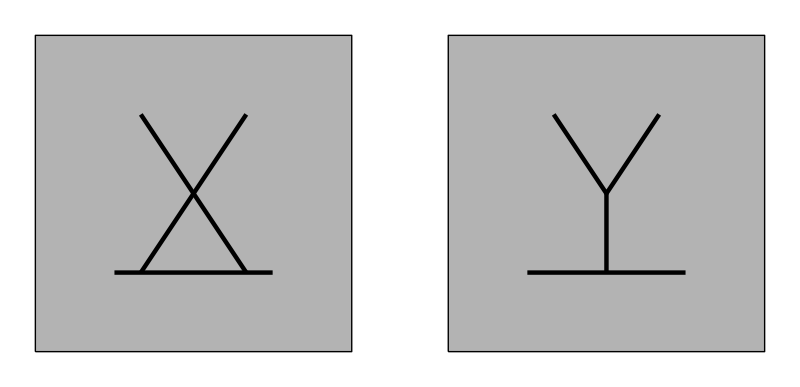

```mathematica
initiators = 
	{{ {GrayLevel[.7], 
	Polygon[{{0,0},{1,0}, {1,1}, {0,1}}]},
	Line[{{0,0},{1,0}, {1,1}, {0,1},{0,0}}],
	{Thickness[.008], 
	Line[{{1/3,1/4},{2/3,3/4}}], 
	Line[{{1/3,3/4},{2/3,1/4}}], 
	Line[{{1/4,1/4},{3/4,1/4}}]}}, 
	{{ {GrayLevel[.7], 
	Polygon[{{0,0},{1,0}, {1,1}, {0,1}}]},
	{Thickness[.008], 
	Line[{{1/3,3/4},{1/2,1/2}, {2/3,3/4}}], 
	Line[{{1/2,1/2},{1/2,1/4}}], 
	Line[{{1/4,1/4},{3/4,1/4}}]},
	Line[{{0,0},{1,0}, {1,1}, {0,1},{0,0}}]}}};
Show[GraphicsArray[
	Graphics[#,AspectRatio -> Automatic]& /@ initiators]]
```

The action of the digraph IFS may now be easily discerned from the following image

GraphicsArray::obs: GraphicsArray is obsolete. Switching to GraphicsGrid.

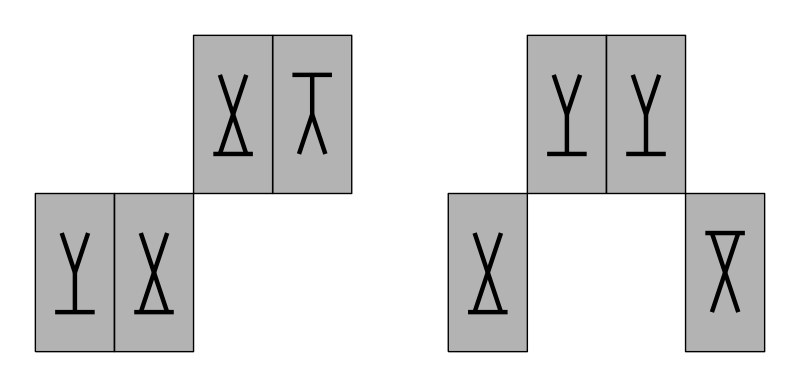

```mathematica
Show[GraphicsArray[
	ShowDigraphFractals[hilbertCurves,1,
	Initiators -> initiators, 
	DisplayFunction -> Identity]]]
```

A proof that these curves are indeed the coordinate functions of Hilbert's curve may be found in [McClure 1999].  For those familiar with Hilbert's curve, here is a convincing graphical argument.  We first generate approximations to our curves using carefully chosen initiators.

```mathematica
twoPoints = {{Point[{1/2,1/2}]},
	{Point[{1/2,1/2}]}};
approximations = 
	ShowDigraphFractals[hilbertCurves,4,
		Initiators -> twoPoints,
		DisplayFunction -> Identity];
```

We can get the actual points as follows

```mathematica
(* Modified for multi-point format *)
graphPoints = Join@@Cases[#,Point[xs_]:>xs,Infinity]& /@ approximations;
```

We then sort these points, collect a list of x versus y, and draw a polygonal line through the resulting list of points.  The result is a familiar approximation to Hilbert's curve.

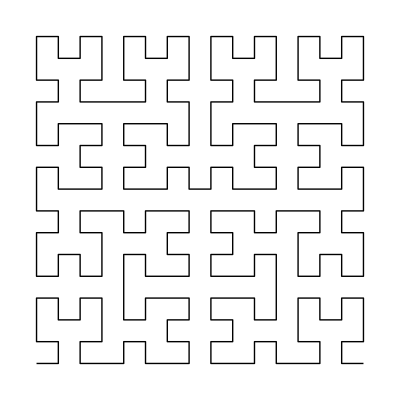

```mathematica
sortedGraphPoints=
	Sort[#,First[#1]<First[#2]&]&/@
	graphPoints;
curvePoints = 
	Transpose[sortedGraphPoints /. 
	{x_Real,y_Real} -> y];
Show[Graphics[Line[curvePoints]],
	AspectRatio -> Automatic]
```

## A Stochastic Algorithm

We now describe a stochastic algorithm similar to the random iteration algorithm for an IFS.  We begin by assigning a positive probability p_e to every e ϵ E such that for every v ϵ V,

∑_(e ϵ E_uv, u ϵ V) p_e = 1.

We then choose an arbitrary point x ϵ ℝ^2, an arbitrary vertex v ϵ V, and some e ϵ E_uv according to our probability list {p_e: e ϵ E_uv, u ϵ V} and apply f_e to x.  If e ϵ E_uv, this gives us a point f_e(x) in our approximation to K_u, which then becomes our new input and the process continues.  We are essentially performing a random walk along the digraph and picking up points as we go along.  The edges are traversed in reverse order since f_e:K_v→K_u when e ϵ E_uv.

We implement this algorithm to generate the digraph fractal curves resulting from a mild variation of our first example.  The main point of the variation is to illustrate the effect of differences in the similarity ratios.  We first define the digraph and transform it into a  digraph containing pure functions.  We also define a probability matrix pMatrix satisfying the conditions described above.  Note that we need the sum of all of the probabilities of all of the edges coming in to any particular node to be 1.  For our matrix representation of the digraph, this means that the sum of all of the probabilities in any column should be 1.  For this reason, it will be convenient to transpose the pMatrix since it is easier to access rows than to access columns.  In this first example, we choose these probabilities to be somewhat arbitrary.

```mathematica
a1 = {{{3/4,0},{0,3/4}},{1/8,√3/8}};
a2 = {1/4 rotate[π/3], {0,0}};
a3 = {1/4 rotate[-π/3],{7/8,√3/8}};
b1 = {{{3/4,0},{0,-3/4}},{1/4,0}};
b2 = {{{1/4,0},{0,1/4}},{0,0}};
newCurvesDigraph = {{{a1},{a2,a3}},{{b1},{b2}}};
toFuncs[{A_,b_}] := N[A.# + b] &;
digraphFuncs = Map[toFuncs,newCurvesDigraph, {3}];
pMatrix = N[{{{1/2},{1/4,1/4}},{{1/2},{1/2}}}];
```

We now need a method to use pMatrix to choose edges according to the scheme described above.  This is based in part on the following technique for choosing a random integer according to a list of probabilities pList.

```mathematica
pList = {.1,.2,.3,.4};
foldedPList = FoldList[Plus,0,pList];
chooser = Random[];
Length[Select[foldedPList,(#< chooser)&]]
```

2

Suppose we are at some vertex v at a point along our random walk.  We will move to the next vertex by first choosing which vertex to move to and then deciding which edge to travel along.  The matrix pMatrix1 will help us make the first of these decisions.  We now transpose pMatrix, add all of the elements in the list in any row and column, and then use FoldList as above.

```mathematica
pMatrix1 = Apply[Plus,Transpose[pMatrix], {2}];
pMatrix1 = FoldList[Plus, 0, #]& /@ pMatrix1;
```

pMatrix2 will help us make the second of our decisions.  To get pMatrix2, we simply normalize the probabilities in the list in any row and column.

```mathematica
pMatrixNormalizer[subPList_List] := 
	FoldList[Plus,0,subPList]/Plus@@subPList;
pMatrix2 = Transpose[Map[pMatrixNormalizer, pMatrix, {2}]];
```

We now write a function choose which will accept a row from pMatrix1 and the corresponding row from pMatrix2 and decide which edge to take.  choose will return an ordered pair of integers {i,j} where i indicates which vertex to travel to and j indicates which edge to take.

```mathematica
choose[v1_,v2_] := Module[
	{i,j, chooser},
	chooser = Random[];
	i = Length[Select[v1,(#< chooser)&]];
	chooser = Random[];
	j = Length[Select[v2[[i]], (#<chooser)&]];
	{i,j}];
```

We now set up an initial configuration and a place to store the points.

```mathematica
v = 1; v1 = pMatrix1[[v]]; v2 = pMatrix2[[v]];
currentPoint = {0,0}; numPoints =3000;
points = Table[{}, {Length[newCurvesDigraph]}];
```

The following Do loop implements the algorithm using the tools we have described.

```mathematica
Do[{
	{i,j} = choose[v1,v2];
	currentPoint = digraphFuncs[[i,v,j]][currentPoint];
	points[[i]] = {points[[i]], currentPoint};
	v = i;  v1 = pMatrix1[[v]];  v2 = pMatrix2[[v]];
	},{numPoints}];
```

Finally, we pass these points to ListPlot.

```mathematica
points = Partition[Flatten[#],2]& /@ points;
ListPlot[#,
	PlotStyle->{AbsolutePointSize[0.5]},
	AspectRatio -> Automatic, 
	Axes -> False]& /@ points;
```

### Determining the probabilities

Our technique seems to have worked, but clearly the images may be improved.  This is because the points are not uniformly distributed throughout the set.  In general, the distribution of the points in the approximation will depend upon the choice of probabilities in pMatrix.  The question arises as to how to choose the probabilities to generate a uniform distribution, which renders the image more efficiently.

In the IFS theory, there is a notion of similarity dimension which coincides with the fractal (Hausdorff) dimension given certain additional assumptions.  A self-similar set is generated by a digraph IFS with one node where to each e ϵ E corresponds a similarity f_e.  If r_e is the similarity ratio of f_e, then the similarity dimension of the self-similar set is the unique s>0 such that

∑_(e ϵ E) r_e^s = 1.

Perhaps not surprisingly, a choice of p_e = r_e^s is the correct way to choose the probabilities to generate this self-similar set efficiently.  It's not unreasonable to suppose that the correct choice of a pMatrix for a digraph IFS will be connected the appropriate notion of dimension.

Suppose we have a digraph IFS such that to each e ϵ E corresponds a similarity f_e with similarity ratio r_e.  For s>0, define a numerical matrix A(s), with rows and columns indexed by V, such that the entry in row u and column v is

A_uv(s) = ∑_(e ϵ E_uv) r_e^s.

The similarity dimension of the digraph IFS is defined to be the unique value of s such that the matrix A(s) has spectral radius 1.  The main result in [Mauldin and Williams 1988] states that this dimension is equal to the Hausdorff dimension of each of the generated digraph fractals under certain additional assumptions.  This theorem is also proved as theorems 6.4.8 and 6.6.6 in [Edgar 1990] and as corollary 3.5 in [Falconer 1997].  An understanding of this proof would help the interested reader understand why our technique for choosing the probabilities works.  The important property of the similarity dimension is that s-dimensional Perron numbers for the digraph IFS exist only for this particular value of s.  These are numbers q_v, indexed by V, such that

q_u^s = ∑_(e ϵ E_uv, v ϵ V) r_e^s q_v^s.

The numbers q_u^s simply form an eigenvector for the matrix A(s) corresponding to the eigenvalue 1.  Note that if we take the transpose of the matrix A(s), find the Perron numbers for this matrix, and then normalize the resulting equations by dividing through by q_u^s, we obtain what appears to be a legitimate pMatrix1.  Taking the transpose simply makes A(s) fit into our algorithm and should pose no difficulty since the transpose preserves the spectral radius.  This is exactly the strategy we will adopt to compute the probabilities

We now implement this plan to compute the matrices pMatrix1 and pMatrix2 directly.  Given an affine function, we will use the spectral radius of the linear part to evaluate the contractivity.  This gives exactly the similarity ratio of a similarity transformation and is roughly the largest scaling factor for a general affine transformation.  Here is the computation of the similarity dimension for the sets A and B.  Note that they should both have the same dimension, since each one contains a self-similar copy of the other.

```mathematica
matrices = Map[First, 
	Transpose[newCurvesDigraph], {3}] // N;
eigenMatrix = matrices /. 
	{{a_Real,b_Real},{c_Real,d_Real}} -> 
	Max[Abs /@ Eigenvalues[{{a,b},{c,d}}]];
sMatrix = Apply[Plus, eigenMatrix^s, {2}];
eigenvalues = Eigenvalues[sMatrix];
spectralRadius0 = Max[Chop[N[eigenvalues /. s -> 0]]];
spectralRadius = Select[eigenvalues, 
	((# /. s ->0) ==spectralRadius0)&][[1]];
approximateDim = Chop[s /.
	FindRoot[spectralRadius == 1, {s,1}]]
```

1.24711

Note that the DigraphFractals package contains the function ComputeDimension which performs this task.

```mathematica
ComputeDimension[newCurvesDigraph]
```

1.24711

We now compute the Perron numbers for the matrix corresponding to this dimension, recalling that these form an eigenvector corresponding to the eigenvalue 1.

```mathematica
dimMatrix = sMatrix /. s -> approximateDim;
Eigensystem[dimMatrix]
```

{{1.,-0.12398},{{0.918145,0.396244},{-0.647324,0.762215}}}

```mathematica
perronNumbers = %[[2]][[1]]
```

{0.918145,0.396244}

Recall that pMatrix1 determines which node to move to from the current node.  This is exactly where we want to use equation 2, which looks like the matrix A(s) times the eigenvector consisting of the Perron numbers.  Thus we use 	Inner to form the equation, but we replace Plus with List so that we may use FoldList to get the result into the form which works with our algorithm.

```mathematica
pMatrix1 = Inner[Times,dimMatrix,
	perronNumbers,List]/perronNumbers;
pMatrix1 = FoldList[Plus, 0, #]& /@ pMatrix1;
```

To obtain pMatrix2, we simply normalize the correct eigenMatrix.

```mathematica
pMatrix2 = eigenMatrix /. s -> approximateDim;
pMatrix2 = Map[pMatrixNormalizer, pMatrix2, {2}];
```

With pMatrix1 and pMatrix2 in hand, the algorithm may now proceed as before.

```mathematica
v = 1; v1 = pMatrix1[[v]]; v2 = pMatrix2[[v]];
currentPoint = {0,0}; numPoints =3000;
points = Table[{}, {Length[newCurvesDigraph]}];
Do[{
	{i,j} = choose[v1,v2];
	currentPoint = digraphFuncs[[i,v,j]][currentPoint];
	points[[i]] = {points[[i]], currentPoint};
	v = i;  v1 = pMatrix1[[v]];  v2 = pMatrix2[[v]];
	},{numPoints}];
points = Partition[Flatten[#],2]& /@ points;
ListPlot[#,
	PlotStyle->{AbsolutePointSize[0.5]},
	AspectRatio -> Automatic, 
	Axes -> False]& /@ points
```

-Graphics-

This is a major improvement.  A close look at these images, however, indicates that the first set is being traced out more heavily than the second.  This is exactly the case, as may be deduced by investigating the Perron numbers.

```mathematica
perronNumbers
```

{0.918145,0.396244}

These numbers indicate the relative "weights" of the sets, so we can see why the first is heavier.  In fact, if we normalize these numbers taking the dimension into account, we should get the exact weights.

```mathematica
perronNumbers^approximateDim/
	Plus@@(perronNumbers^approximateDim)
```

{0.740387,0.259613}

The following computation indicates that this has worked very well.

```mathematica
(Length /@ points)/numPoints // N
```

{0.745,0.255}

This technique for choosing the probabilities is encoded in the package function ComputePMatrix, which goes further and combines the pMatrix1 and pMatrix2 obtained above into one pMatrix.  Here is the pMatrix for our sets.

```mathematica
ComputePMatrix[newCurvesDigraph]
```

{{{0.698534},{0.411257,0.411257}},{{0.301466},{0.177486}}}

## More Examples

Our stochastic algorithm is encapsulated in the package function ShowDigraphFractalsStochastic.  In this section, we illustrate the use of this function.  The option PMatrix may be used to specify the probabilities for the algorithm and PMatrix → Automatic generates the probabilities automatically.  Here is the package description of the function ShowDigraphFractalsStochastic.

```mathematica
?ShowDigraphFractalsStochastic
```

ShowDigraphFractalsStochastic[digraph_,numPoints_] generates numPoints points approximating the digraph Self Similar sets defined by digraph using a stochastic algorithm. The digraph is represented by a matrix of lists of affine functions written in the form {{{a1,a2},{b1,b2}},{x0,y0}}.

### The Mauldin–Williams curves

Our first example is the digraph IFS for curves called the Mauldin–Williams curves in [Edgar 1990].  This example shows that our algorithm works on a digraph with more than two nodes.

```mathematica
a1 = {{{1/2,0},{0,-1/2}},{0,0}};
a2 = {{{1/2,0},{0,-1/2}},{1/2,0}};
α = ArcCos[17/18];  β = ArcCos[1/6];
b1 = {(1/3) rotate[-β], {Cos[α], Sin[α]}};
b2 = {rotate[α], {0,0}};
c1 = {{{1/4,0},{0,-1/4}},{0,0}};
c2 = {{{3/4,0},{0,-3/4}},{1/4,0}};
MWCurves = { {{a1},{a2},{}},
			{{b1},{},{b2}},
			{{},{c1},{c2}} };
```

```mathematica
ShowDigraphFractalsStochastic[MWCurves,6000]
```

-Graphics-

### A self-similar spiral

For our next example, we generate a self-similar spiral.  This example shows that our technique works for a one-node digraph.  The rotation in the transformation a1 involves the golden ratio so that the resulting image has a double spiral appearance: 13 spirals in the clockwise direction and 21 in the counterclockwise direction.  For a discussion on how the double spiral arises and the connection with the golden ratio and Fibonacci numbers, see chapter 9 of [Stewart 1995].

```mathematica
goldenAngle=2π(2-GoldenRatio);
a1 = {.985 rotate[goldenAngle], {0.,0.}};
a2 = {{{.1,0},{0,.1}}, {1,0.}};
spiral = {{{a1,a2}}};
```

```mathematica
ShowDigraphFractalsStochastic[spiral,20000]
```

-Graphics-

### Enhancing the self-similar spiral

There are a few variations on the double spiral theme.  Here is an example of two digraph self-similar spirals related to our last spiral.  Note that for the second spiral below we change the angle of rotation just slightly.  The resulting effect on the spiral is dramatic in the sense that the double spiral appearance is completely gone.

```mathematica
a1 = {.985 rotate[goldenAngle], {0.,0.}};
b1 = {.95 rotate[goldenAngle - 0.05], {0.,0.}};
a2 = b2 = {{{.1,0},{0,.1}}, {1,0.}};
spirals = {{{a1},{a2}},{{b2},{b1}}};
```

```mathematica
ShowDigraphFractalsStochastic[spirals,30000]
```

-Graphics-

For our final example, we highlight every third spiral of the 21 spirals in the counterclockwise direction.

```mathematica
s1 = {.985^3 rotate[3goldenAngle],{0,0}};
s2 = {{{.1,0},{0,.1}},{1,0}};
d1 = {{{.1,0},{0,.1}},.985 rotate[goldenAngle].{1,0}};
d2 = {{{.1,0},{0,.1}},.985^2 rotate[2goldenAngle].{1,0}};
d3 = s1;
intertwinedSpirals = {{{s1},{s2}},{{d1,d2},{d3}}};
ShowDigraphFractalsStochastic[
	intertwinedSpirals,30000]
```

-Graphics-

We can see why the name intertwinedSpiral was used as follows.

```mathematica
Show[%]
```

-Graphics-

An image very similar to this appears on the cover of [Falconer 1997].

## References

Barnsley, M.F.  1993.  Fractals Everywhere  2nd ed.,  Academic Press  Boston.

Edgar, G.A.  1990.  Measure, Topology, and Fractal Geometry.  Springer-Verlag  New York.

Falconer, K.J. 1997. Techniques in Fractal Geometry.  John Wiley and Sons  West Sussex, England.

Gutierrez, J.M., Iglesias, A., Rodriguez, M.A., and Rodriguez, V.J.  1997.  Generating and rendering fractal images.  The Mathematica Journal.  7(1):6–13.

Mauldin, R.D. and Williams, S.C.  1988.  Hausdorff dimension in graph directed constructions.  Trans. Amer. Math. Soc.  309:811–829.

McClure, M.  1999.  Directed-graph fractal structure in space-filling curves.  Submitted to Math. Mag.

Stewart, I.  1995.  Nature's Numbers.  Basic Books  New York.

## About the Author

Mark McClure is an assistant professor of mathematics at the University of North Carolina at Asheville.  He received his Ph.D. in mathematics from the Ohio State University under the direction of Gerald Edgar.  His primary research interest is the study of fractal dimensions of various sets arising in real analysis.  He was introduced to Mathematica through the Calculus&Mathematica program at OSU.

Mark McClure
Department of Mathematics
University of North Carolina at Asheville
Asheville, North Carolina 28804
mcmcclur@bulldog.unca.edu
http://www.unca.edu/~mcmcclur/